# EQLab package quick guide.

## Useful Info

1) Some definitions:

1.1) USER         →    one of us, someone who runs this package.

1.2) predictor → an expert, a person whose behaviour/belief we try to model

1.3) question  →  a  basic  ‘unit’ in an experiment, indexed by ‘i’.  Asking a question (fixed i) is  step that involves producing:
	a) forecasts  p_ij for each predictor ( for all values of   j )
	b) a measurement m_i (like tossing a die)
	c) resolutions v_ij for each predictor  ( for all values of   j ) 
	d) outcome q_i ( this reflects the resolution of the majority of predictors  )
	e) surprisals s_ij for each predictor  ( for all values of   j ) 
	f)  rewards r_ij  for each predictor  ( for all values of   j )  
	A question is stored in EQLab as a List :  question_i={p_i,m_i,v_i,q,s_i,r_i};  Where bold letters are each a List
	
1.4) Experiment → a set of questions asked in sequence (stored as a List of questions)

2)Some variable definitions:

2.1) npredictors →  number of  predictors  (cannot be modified after loading EQLab )
         nquestions →  number of  questions for each experiment (can be modified in between experiments)

2.2) npredictorsUSER →   number of  predictors, to be defined by user before  loading EQLab. (have no effect after loading)

## Steps to prepare simulations

Set user parameter values

```mathematica
npredictorsUSER=4;
```

Load package

```mathematica
$Path=Join[$Path,{NotebookDirectory[]}];
<<EQLab`
```

Define functions needed for experiment. Needs the follow the prototypes below:

UserPredict[exp_]       →  Function should return a List of numbers (forecasts) of size ‘npredictors’ ;    ‘exp’  is  an experiment as defined in EQLab and it is useful if predictors update their forecast based on previous questions (as in this example).

```mathematica
(*set initial forecast*)
setforecastinit[]:=(forecastinit=Table[Random[],{i,1,npredictors}];);
forecastinit={9/10,5/10,1/10,1/10}//N;
(*random numbers M to model how each predictor 'reacts' for previous measurements*)
(*smaller M means more reactive*)
setreactioninit[]:=(reactivity=Table[RandomInteger[{1,20}],{i,1,npredictors}];)
reactivity={1,100,1,100};
UserPredict[exp_]:=Module[
{REACTIVITY=reactivity,M,ipredictor,n=(exp//Length),ρnew,ρ,m,RHOnew={}},


For[ipredictor=1,ipredictor≤npredictors,ipredictor++,
If[n==0,
ρnew=forecastinit[[ipredictor]],
ρ=exp[[n,1,ipredictor]];
m=exp[[n,2]];
M=REACTIVITY[[ipredictor]];
ρnew=1/(2 (M+n))+m/(2 (M+n))+((-1+M+n) ρ)/(M+n);
];
AppendTo[RHOnew,ρnew];];
RHOnew]
```

UserMeasure[] 	      →    Function should return either    +1 or -1.  (yes or no, like the toss of a die.)

```mathematica
prob=7/10;
UserMeasure[]:=(Random[]//Which[#<prob,1,True,-1]&);
```

UserResolve[exp_ , newquestion_]  	      →    Function should use the List  ‘newquestion[[2]]’ ( forecasts), and  return a List of numbers (resolutions) of the same size.  Arguments are   an experiment  and a question  as defined in EQLab. The variable ‘exp’ is useful only when modeling predictors that use knowledge from previous  questions in the experiment. Even If ‘exp’ is not used, the function must adhere to the  prototype.

```mathematica
UserResolve[experiment_,question_]:=UserResolve[question];
UserResolve[question_]:=Table[Random[]//Which[#<0.0,-question[[2]],True,question[[2]]]&,{i,1,question[[1]]//Length}]
```

## Perform Experiments

#### Results of experiments are stored in the List called ‘EXPERIMENT’

```mathematica
EXPERIMENT
```

{}

#### By default, EQLab loads some predefined functions, So you can run an experiment.

```mathematica
RunExperiment[]
```

#### Now EXPERIMENT has one element (one experiment)

```mathematica
EXPERIMENT[[1,All,6]][[1]]//Length
```

4

```mathematica
EXPERIMENT//Length
```

1

#### One can run another experiment, and check the size of EXPERIMENT again

```mathematica
RunExperiment[]
EXPERIMENT//Length
```

2

#### See contents of experiment 1

```mathematica
EXPERIMENT[[1]]
```

{{{0.818004,0.992891,0.363268,0.846631},-1,{-1,-1,-1,-1},-1,{1.70377,4.94632,0.451407,1.87491},{4.68003,0.,7.07202,4.35316}},{{0.818004,0.992891,0.363268,0.846631},-1,{-1,-1,-1,-1},-1,{1.70377,4.94632,0.451407,1.87491},{4.68003,0.,7.07202,4.35316}},{{0.818004,0.992891,0.363268,0.846631},-1,{-1,-1,-1,-1},-1,{1.70377,4.94632,0.451407,1.87491},{4.68003,0.,7.07202,4.35316}},{{0.818004,0.992891,0.363268,0.846631},-1,{1,-1,-1,-1},-1,{1.70377,4.94632,0.451407,1.87491},{2.34001,0.,3.53601,2.17658}},{{0.818004,0.992891,0.363268,0.846631},1,{1,1,1,1},1,{0.200888,0.00713488,1.01261,0.16649},{0.270082,0.357628,0.,0.285624}},{{0.818004,0.992891,0.363268,0.846631},-1,{-1,-1,-1,-1},-1,{1.70377,4.94632,0.451407,1.87491},{4.68003,0.,7.07202,4.35316}},{{0.818004,0.992891,0.363268,0.846631},1,{1,1,1,1},1,{0.200888,0.00713488,1.01261,0.16649},{0.270082,0.357628,0.,0.285624}},{{0.818004,0.992891,0.363268,0.846631},1,{1,1,1,1},1,{0.200888,0.00713488,1.01261,0.16649},{0.270082,0.357628,0.,0.285624}},{{0.818004,0.992891,0.363268,0.846631},-1,{-1,-1,-1,-1},-1,{1.70377,4.94632,0.451407,1.87491},{4.68003,0.,7.07202,4.35316}},{{0.818004,0.992891,0.363268,0.846631},-1,{-1,-1,-1,-1},-1,{1.70377,4.94632,0.451407,1.87491},{4.68003,0.,7.07202,4.35316}},{{0.818004,0.992891,0.363268,0.846631},-1,{-1,-1,-1,-1},-1,{1.70377,4.94632,0.451407,1.87491},{4.68003,0.,7.07202,4.35316}},{{0.818004,0.992891,0.363268,0.846631},1,{1,-1,1,1},1,{0.200888,0.00713488,1.01261,0.16649},{0.135041,0.178814,0.,0.142812}},{{0.818004,0.992891,0.363268,0.846631},1,{1,1,1,1},1,{0.200888,0.00713488,1.01261,0.16649},{0.270082,0.357628,0.,0.285624}},{{0.818004,0.992891,0.363268,0.846631},-1,{-1,-1,1,-1},-1,{1.70377,4.94632,0.451407,1.87491},{2.34001,0.,3.53601,2.17658}},{{0.818004,0.992891,0.363268,0.846631},-1,{-1,-1,-1,-1},-1,{1.70377,4.94632,0.451407,1.87491},{4.68003,0.,7.07202,4.35316}},{{0.818004,0.992891,0.363268,0.846631},-1,{-1,-1,-1,-1},-1,{1.70377,4.94632,0.451407,1.87491},{4.68003,0.,7.07202,4.35316}},{{0.818004,0.992891,0.363268,0.846631},1,{1,1,1,1},1,{0.200888,0.00713488,1.01261,0.16649},{0.270082,0.357628,0.,0.285624}},{{0.818004,0.992891,0.363268,0.846631},-1,{-1,-1,-1,-1},-1,{1.70377,4.94632,0.451407,1.87491},{4.68003,0.,7.07202,4.35316}},{{0.818004,0.992891,0.363268,0.846631},1,{1,1,1,1},1,{0.200888,0.00713488,1.01261,0.16649},{0.270082,0.357628,0.,0.285624}},{{0.818004,0.992891,0.363268,0.846631},-1,{-1,-1,-1,-1},-1,{1.70377,4.94632,0.451407,1.87491},{4.68003,0.,7.07202,4.35316}}}

#### MakePlots[i] does the plots for the ith experiment and stores it in a ‘SUPERARRAY‘ called ‘PLOTS’. Use ShowPlots[i] to see results.

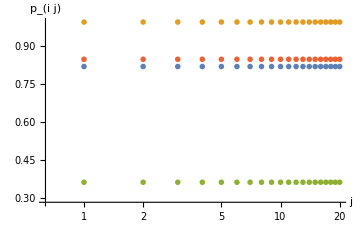
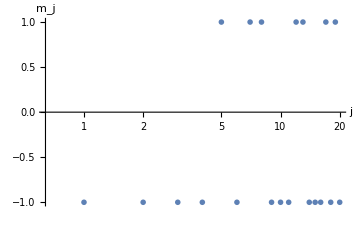
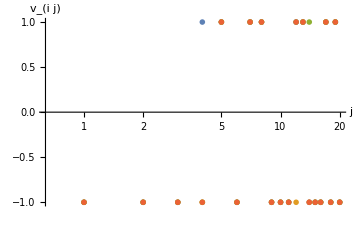
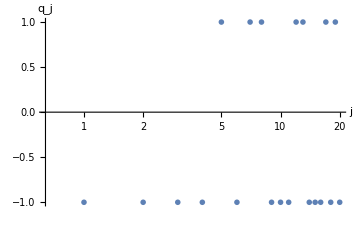
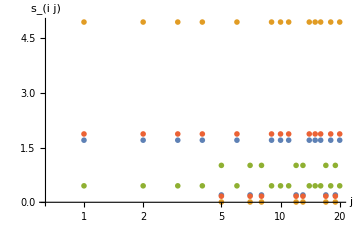
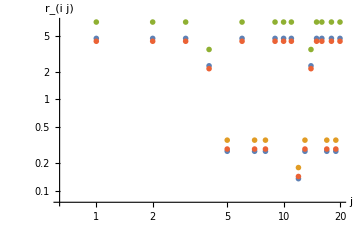
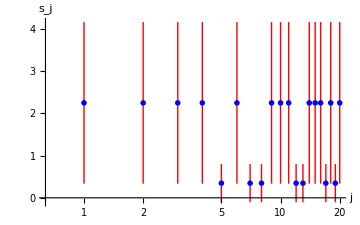
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- |  |

```mathematica
MakePlots[1]
ShowPlots[1]
```

#### Experiments 1 and 2 where done with default functions and default values for ‘nquestions’. To use the custom functions defined above, one needs to load them with ‘SetUserFunctions[]’

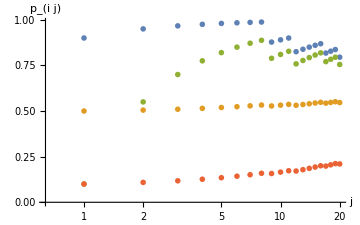
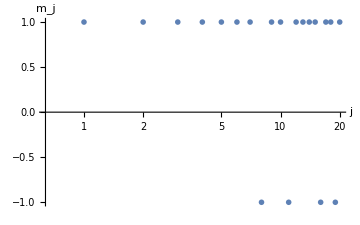
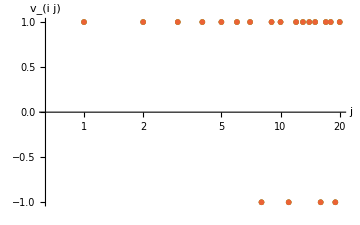
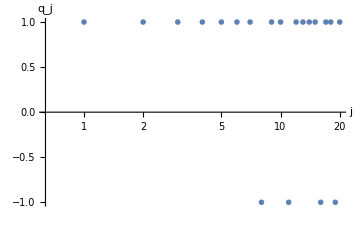
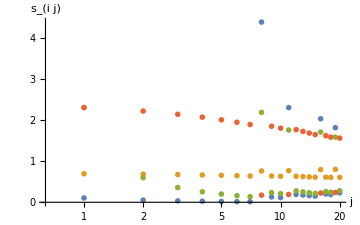
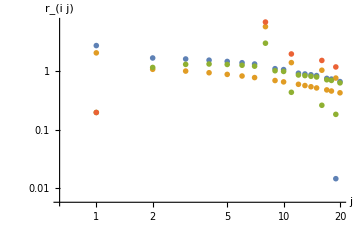
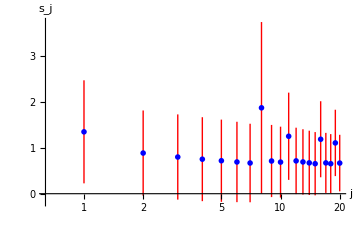
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- |  |

```mathematica
SetUserFunctions[]
RunExperiment[]
MakePlots[3]
ShowPlots[3]
```

#### ‘qpredictors’ cannot be changed, but ‘nquestions’ can be reinitialized before running another experiment

```mathematica
(*EXPERIMENT=EXPERIMENT//Delete[-1]//Length*)
```

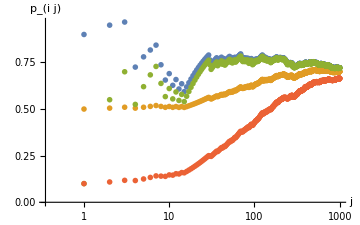
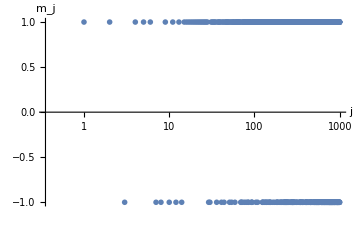
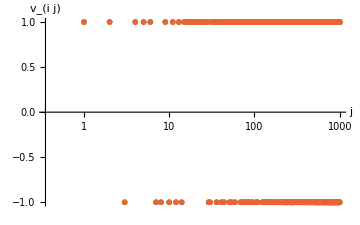
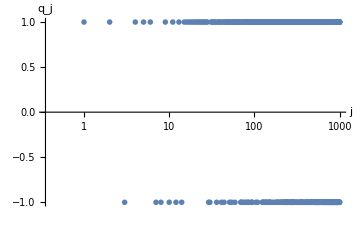
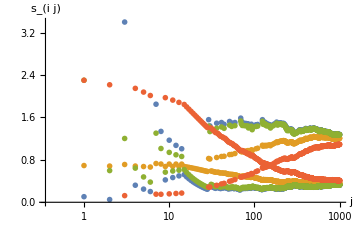
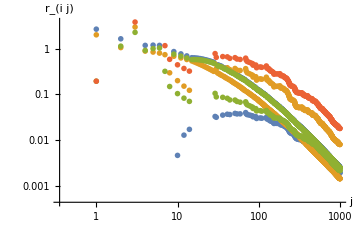
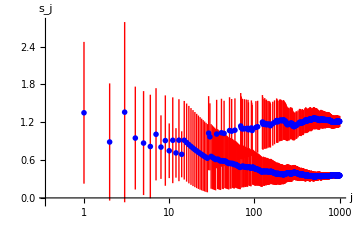
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- |  |

```mathematica
nquestions=1000;
RunExperiment[]
MakePlots[4]
ShowPlots[4]
```

#### work in progress: cumulative rewards (here for last experiment, with user functions)

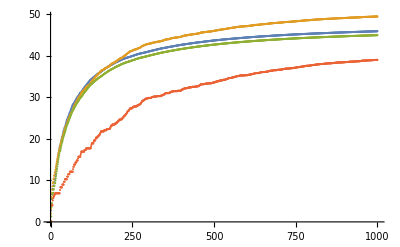

```mathematica
Cumulative[array_]:=Module[
{i,output={array[[1]]},size=array//Length,c},

For[i=2,i≤ size,i++,
c=array[[i]]+output[[i-1]];
AppendTo[output,c];

];
output//N
]
r1=EXPERIMENT[[4,All,6]][[All,1]]//Cumulative;
r2=EXPERIMENT[[4,All,6]][[All,2]]//Cumulative;r3=EXPERIMENT[[4,All,6]][[All,3]]//Cumulative;r4=EXPERIMENT[[4,All,6]][[All,4]]//Cumulative;
ListPlot[{r1,r2,r3,r4}]
```